# Bitcoin ROI performance

```mathematica
Clear["Global`"];
(*Buttons to hide/show code*)
CloseAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];
SetOptions[#,CellOpen->False]&/@cells;];

OpenAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];
SetOptions[#,CellOpen->True]&/@cells;];

Row[{Button["Hide Code",SelectionEvaluate[CloseAllInputsCells[]]],Button["Show Code",SelectionEvaluate[OpenAllInputsCells[]]]}]
```

Hide CodeShow Code

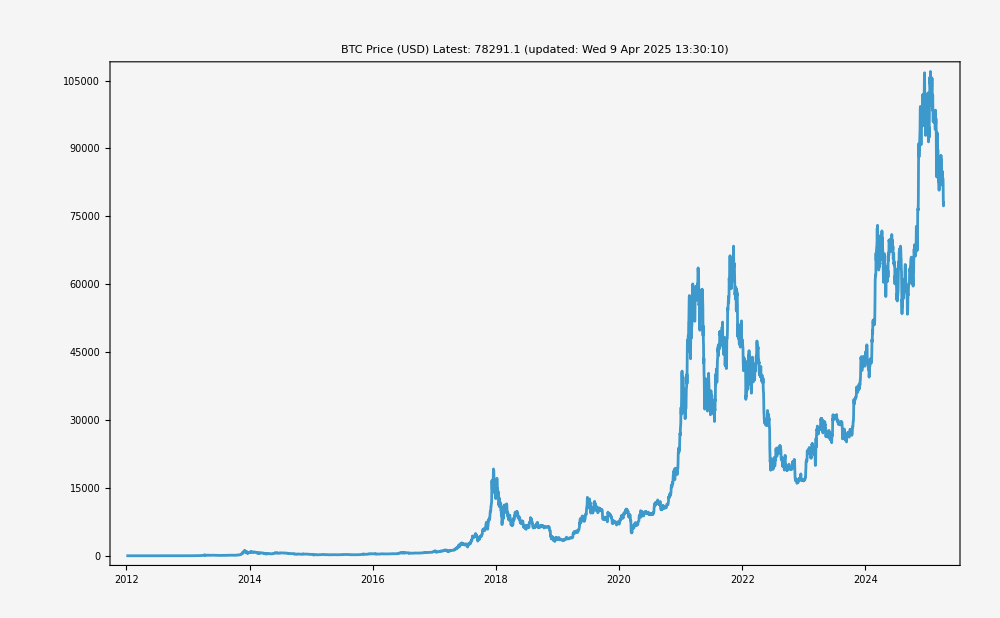

```mathematica
SetDirectory[NotebookDirectory[]];
btc=FinancialData["BTC/USD",{2012,1,1}];
price = Last[Last[btc//Normal]];
pl[x_]:=Style[x,{16,Bold,Red}]
settings=<|
drop->180
,imagemargins->20
,imagesize->1000
,labelstyle->Directive[14]
,plotbackground->Lighter[LightGray,0.75]
,subtitlestyle -> {15}
,ticksstyle->Directive[{16}]
,titlestyle->{20,Red}
|>;
updatedstr=Style[StringTemplate["(updated: ``)"][DateString[]],settings[subtitlestyle]];

DateListPlot[
btc
,PlotLabel->Column[{
Style["BTC Price (USD)",settings[titlestyle]]
,Style[StringForm["Latest: ``", ToString[btc["LastValue"]]],settings[subtitlestyle]]
,updatedstr
},
Center
]
,Background->settings[plotbackground]
,GridLines->{Automatic,Range[0,1000000,5000]}
,Ticks->Automatic
,ImageMargins->settings[imagemargins]
,ImageSize->settings[imagesize]
,FrameTicks->All
,FrameTicksStyle-> settings[ticksstyle]
]
```

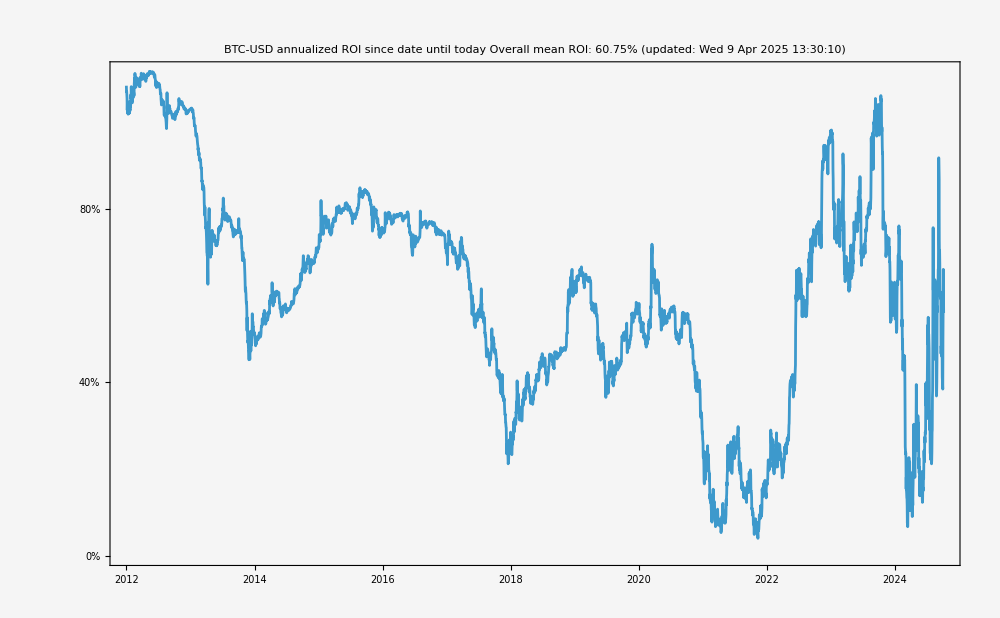

```mathematica
intermediate={#[[1]],#[[2]],UnitConvert[Today-#[[1]],"Years"],1+(price - #[[2]])/(#[[2]])}&/@Normal[btc];
roi={#[[1]],(#[[4]]^(1/QuantityMagnitude[#[[3]]]))-1}&/@ Drop[intermediate,-1];
plotdata = Drop[roi,-settings[drop]];
overallmean=Last/@plotdata//Mean;
btcroiperformance=DateListPlot[plotdata
,PlotLabel->Column[{
Style["BTC-USD annualized ROI since date until today",settings[titlestyle]]
,Style[StringForm["Overall mean ROI: ``",PercentForm[overallmean]],settings[subtitlestyle]]
,updatedstr
}
,Center
]
,Background->settings[plotbackground]
,GridLines->{Automatic, Join[Range[-5,50,0.1],{#,Thick}&/@ Range[0,50,0.5]]}
,ImageSize->settings[imagesize]
,ImageMargins->settings[imagemargins]
, PlotRange->Full
,FrameTicks->{Automatic,Table[{x,Style[PercentForm[x],{16}]},{x,0,5,0.1}]}
,FrameTicksStyle-> settings[ticksstyle]
,Ticks->{Automatic, Range[0,2,0.01]}
];
filename = "BTC-ROI-Performance.jpg";
Export[filename,btcroiperformance];
btcroiperformance
```

```mathematica
yrs=GroupBy[plotdata,DateValue[First[#],"Year"]&];
yravg=AssociationThread[DateObject[{#}]&/@Keys[yrs] -> Table[Last/@ yrs[yr]//Mean,{yr,Keys[yrs]}]];
btcyearlyroiperformance=DateListPlot[
Callout[#,PercentForm[Last[#]]]&/@KeyValueMap[List,yravg]
,PlotLabel->Column[{
Style["BTC-USD average ROI, bought year to today", settings[titlestyle]]
,Style[StringForm["Overall mean ROI: ``",PercentForm[overallmean]],settings[subtitlestyle]]
,updatedstr
},
Center
]
,Joined->False
,Background->settings[plotbackground]
,GridLines->{
DateRange[DateObject[{2010,1,1}],DateObject[{2030,1,1}], {1, "Year"}] 
,Join[Range[-5,50,0.1],{#,Thick}&/@ Range[0,50,0.1]]
}
,Frame->True
,ImageSize->settings[imagesize]
,ImageMargins->settings[imagemargins]
,PlotRange->Full
,FrameTicks->{Automatic,Table[{x,Style[PercentForm[x],{16}]},{x,0,5,0.1}]}
,FrameTicksStyle-> settings[ticksstyle]
];
filename = "BTC-Yearly-ROI-Performance.jpg";
Export[filename,btcyearlyroiperformance];
btcyearlyroiperformance
```

-Graphics-